## post-refinement visualization

```mathematica
fileSEG = "C:\\Users\\Ali Hashmi\\Desktop\\3D segmentation fixed spheroid\\C0.res2";
Get[fileSEG];
```

```mathematica
Colorize@segNew
```

-Graphics3D-

```mathematica
{cellnum,{minarea,maxarea}}=ComponentMeasurements[segNew,"Area"][[All,2]]//{Length[#],MinMax[#]}&
```

{412,{774.25,23445.9}}

```mathematica
primaryStats[seg_]:= Module[{areasM,avgcellsize,areaval},
areasM =ComponentMeasurements[seg,#]&@"Area";
Print["total number of nuclei: ",Length@areasM];
areaval = areasM[[All,2]];
Print[Style["average cell area in pixels: ",{Bold,Red,FontSize-> 14}],Style[avgcellsize= Mean@areaval,{Bold,FontSize->15}]];
Print@SmoothHistogram[areaval/avgcellsize,PlotStyle->{Thick,XYZColor[0,0,1,0.8]},PlotLabel->"probable nuclei per blob"];
Print@ListPlot[areaval/avgcellsize,PlotStyle->{XYZColor[0,0,1,0.6],PointSize[Large]},PlotLabel->"probable nuclei per blob"];
]
```

total number of nuclei: 412

average cell area in pixels: 8181.2

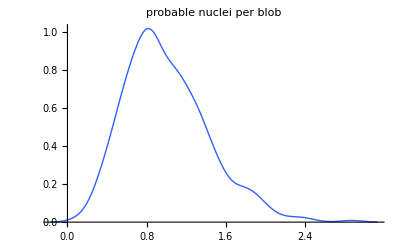

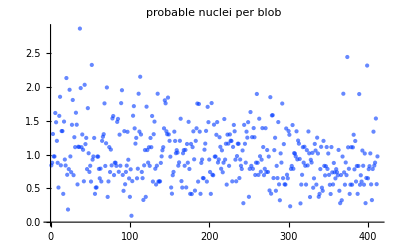

```mathematica
primaryStats[segNew]
```

### original image stack visualization

```mathematica
initialStackData[file_]:=Module[{bc,bc3d,roi},
bc=Import@file;
bc3d= Image3D[bc];
roi=Sequence@@Thread[{1,Reverse@ImageDimensions[bc3d]}];
bc3d=ImageTake[bc3d,roi];
Print[ImageAdjust@bc3d];
{{roi},ImageData[bc3d]}
];
```

```mathematica
file = "C:\\Users\\Ali Hashmi\\Desktop\\3D segmentation fixed spheroid\\C0.tif";
{roi,imgdata}=initialStackData@file;
```

-Graphics3D-

```mathematica
(* Now lets fill holes in the raw image *)
```

```mathematica
fillHoles[imgdata_,size_]:= DeleteSmallComponents[FillingTransform@Image[imgdata],size]//ImageData;
```

```mathematica
height=roi[[1,2]]
```

54

```mathematica
Do[imgdata[[i]] = fillHoles[imgdata[[i]],20],{i,height}];
img= Image3D[imgdata]//DeleteSmallComponents[#,100]&
(* here we fill holes and delete small components from the data *)
```

-Graphics3D-

```mathematica
imgdata=ImageData@img; (* data after filling holes and deleting small components *)
```

## visualizing refined nuclei

```mathematica
newArray=Module[{imgdata=imgdata,array,cellnum=cellnum,seg=segNew,cellpos,pixelvals,roi=roi},
array=ConstantArray[0,{roi[[1,2]],roi[[2,2]],roi[[3,2]]}]; (* initially empty designed to hold nuclei *)
Do[
Print["processing: ", i];
cellpos=Position[seg,i];
pixelvals = Extract[imgdata,cellpos];
array=ReplacePart[array,Thread[cellpos->pixelvals]]
,{i,Range@cellnum}
];
array
];
```

processing: 1

processing: 2

processing: 3

processing: 4

processing: 5

processing: 6

processing: 7

processing: 8

processing: 9

processing: 10

processing: 11

processing: 12

processing: 13

processing: 14

processing: 15

processing: 16

processing: 17

processing: 18

processing: 19

processing: 20

processing: 21

processing: 22

processing: 23

processing: 24

processing: 25

processing: 26

processing: 27

processing: 28

processing: 29

processing: 30

processing: 31

processing: 32

processing: 33

processing: 34

processing: 35

processing: 36

processing: 37

processing: 38

processing: 39

processing: 40

processing: 41

processing: 42

processing: 43

processing: 44

processing: 45

processing: 46

processing: 47

processing: 48

processing: 49

processing: 50

processing: 51

processing: 52

processing: 53

processing: 54

processing: 55

processing: 56

processing: 57

processing: 58

processing: 59

processing: 60

processing: 61

processing: 62

processing: 63

processing: 64

processing: 65

processing: 66

processing: 67

processing: 68

processing: 69

processing: 70

processing: 71

processing: 72

processing: 73

processing: 74

processing: 75

processing: 76

processing: 77

processing: 78

processing: 79

processing: 80

processing: 81

processing: 82

processing: 83

processing: 84

processing: 85

processing: 86

processing: 87

processing: 88

processing: 89

processing: 90

processing: 91

processing: 92

processing: 93

processing: 94

processing: 95

processing: 96

processing: 97

processing: 98

processing: 99

processing: 100

processing: 101

processing: 102

processing: 103

processing: 104

processing: 105

processing: 106

processing: 107

processing: 108

processing: 109

processing: 110

processing: 111

processing: 112

processing: 113

processing: 114

processing: 115

processing: 116

processing: 117

processing: 118

processing: 119

processing: 120

processing: 121

processing: 122

processing: 123

processing: 124

processing: 125

processing: 126

processing: 127

processing: 128

processing: 129

processing: 130

processing: 131

processing: 132

processing: 133

processing: 134

processing: 135

processing: 136

processing: 137

processing: 138

processing: 139

processing: 140

processing: 141

processing: 142

processing: 143

processing: 144

processing: 145

processing: 146

processing: 147

processing: 148

processing: 149

processing: 150

processing: 151

processing: 152

processing: 153

processing: 154

processing: 155

processing: 156

processing: 157

processing: 158

processing: 159

processing: 160

processing: 161

processing: 162

processing: 163

processing: 164

processing: 165

processing: 166

processing: 167

processing: 168

processing: 169

processing: 170

processing: 171

processing: 172

processing: 173

processing: 174

processing: 175

processing: 176

processing: 177

processing: 178

processing: 179

processing: 180

processing: 181

processing: 182

processing: 183

processing: 184

processing: 185

processing: 186

processing: 187

processing: 188

processing: 189

processing: 190

processing: 191

processing: 192

processing: 193

processing: 194

processing: 195

processing: 196

processing: 197

processing: 198

processing: 199

processing: 200

processing: 201

processing: 202

processing: 203

processing: 204

processing: 205

processing: 206

processing: 207

processing: 208

processing: 209

processing: 210

processing: 211

processing: 212

processing: 213

processing: 214

processing: 215

processing: 216

processing: 217

processing: 218

processing: 219

processing: 220

processing: 221

processing: 222

processing: 223

processing: 224

processing: 225

processing: 226

processing: 227

processing: 228

processing: 229

processing: 230

processing: 231

processing: 232

processing: 233

processing: 234

processing: 235

processing: 236

processing: 237

processing: 238

processing: 239

processing: 240

processing: 241

processing: 242

processing: 243

processing: 244

processing: 245

processing: 246

processing: 247

processing: 248

processing: 249

processing: 250

processing: 251

processing: 252

processing: 253

processing: 254

processing: 255

processing: 256

processing: 257

processing: 258

processing: 259

processing: 260

processing: 261

processing: 262

processing: 263

processing: 264

processing: 265

processing: 266

processing: 267

processing: 268

processing: 269

processing: 270

processing: 271

processing: 272

processing: 273

processing: 274

processing: 275

processing: 276

processing: 277

processing: 278

processing: 279

processing: 280

processing: 281

processing: 282

processing: 283

processing: 284

processing: 285

processing: 286

processing: 287

processing: 288

processing: 289

processing: 290

processing: 291

processing: 292

processing: 293

processing: 294

processing: 295

processing: 296

processing: 297

processing: 298

processing: 299

processing: 300

processing: 301

processing: 302

processing: 303

processing: 304

processing: 305

processing: 306

processing: 307

processing: 308

processing: 309

processing: 310

processing: 311

processing: 312

processing: 313

processing: 314

processing: 315

processing: 316

processing: 317

processing: 318

processing: 319

processing: 320

processing: 321

processing: 322

processing: 323

processing: 324

processing: 325

processing: 326

processing: 327

processing: 328

processing: 329

processing: 330

processing: 331

processing: 332

processing: 333

processing: 334

processing: 335

processing: 336

processing: 337

processing: 338

processing: 339

processing: 340

processing: 341

processing: 342

processing: 343

processing: 344

processing: 345

processing: 346

processing: 347

processing: 348

processing: 349

processing: 350

processing: 351

processing: 352

processing: 353

processing: 354

processing: 355

processing: 356

processing: 357

processing: 358

processing: 359

processing: 360

processing: 361

processing: 362

processing: 363

processing: 364

processing: 365

processing: 366

processing: 367

processing: 368

processing: 369

processing: 370

processing: 371

processing: 372

processing: 373

processing: 374

processing: 375

processing: 376

processing: 377

processing: 378

processing: 379

processing: 380

processing: 381

processing: 382

processing: 383

processing: 384

processing: 385

processing: 386

processing: 387

processing: 388

processing: 389

processing: 390

processing: 391

processing: 392

processing: 393

processing: 394

processing: 395

processing: 396

processing: 397

processing: 398

processing: 399

processing: 400

processing: 401

processing: 402

processing: 403

processing: 404

processing: 405

processing: 406

processing: 407

processing: 408

processing: 409

processing: 410

processing: 411

processing: 412

```mathematica
Image3D@newArray
```

-Graphics3D-

## save nuclei visualization

```mathematica
filesave = StringReplace[file,"C0.tif"-> "nucleivisualization.res3"];
Save[filesave,{segNew}]
```